```mathematica
Subt[list_]:=-(Plus@@list-2list[[1]])
```

```mathematica
Divi[list_]:=Times@@(list[[1]]*1/list[[2;;]])
```

```mathematica
F[a_,b_,x_]:=Module[{fi=FactorInteger[x],ops={a,b}},

If[ops=={-2,-2},Return[Divi@(Divi/@fi)]];
If[ops=={-2,-1},Return[Divi@(Subt/@fi)]];
If[ops=={-2,1},Return[Divi@(Plus@@@fi)]];
If[ops=={-2,2},Return[Divi@(Times@@@fi)]];
If[ops=={-2,3},Return[Divi@(Power@@@fi)]];

If[ops=={-1,-2},Return[Subt@(Divi/@fi)]];
If[ops=={-1,-1},Return[Subt@(Subt/@fi)]];
If[ops=={-1,1},Return[Subt@(Plus@@@fi)]];
If[ops=={-1,2},Return[Subt@(Times@@@fi)]];
If[ops=={-1,3},Return[Subt@(Power@@@fi)]];

If[ops=={1,-2},Return[Plus@@Divi/@fi]];
If[ops=={1,-1},Return[Plus@@Subt/@fi]];
If[ops=={1,1},Return[Plus@@Plus@@@fi]];
If[ops=={1,2},Return[Plus@@Times@@@fi]];
If[ops=={1,3},Return[Plus@@Power@@@fi]];

If[ops=={2,-2},Return[Times@@Divi/@fi]];
If[ops=={2,-1},Return[Times@@Subt/@fi]];
If[ops=={2,1},Return[Times@@Plus@@@fi]];
If[ops=={2,2},Return[Times@@Times@@@fi]];
If[ops=={2,3},Return[Times@@Power@@@fi]];

If[ops=={3,-2},Return[Power@@Divi/@fi]];
If[ops=={3,-1},Return[Power@@Subt/@fi]];
If[ops=={3,1},Return[Power@@Plus@@@fi]];
If[ops=={3,2},Return[Power@@Times@@@fi]];
If[ops=={3,3},Return[Power@@Power@@@fi]];
]
```

```mathematica
G[n_]:=Module[{},
range={-2,-1,1,2};
pp=Range[n^2];
qq=Flatten[Table[{s,t},{s,range},{t,range}],1];
xticks=Transpose[{Range@(2n+1),Range[-n,n]}];
yticks={};
For[i=1,i≤Length[range]^2,i++,AppendTo[yticks,{pp[[i]],qq[[i]]}]];
Quiet[ArrayPlot[Flatten[Table[F[a,b,x],{a,range},{b,range},{x,-n,n}],1],FrameTicks->{yticks,{{n+1,0}}}]]
]
```

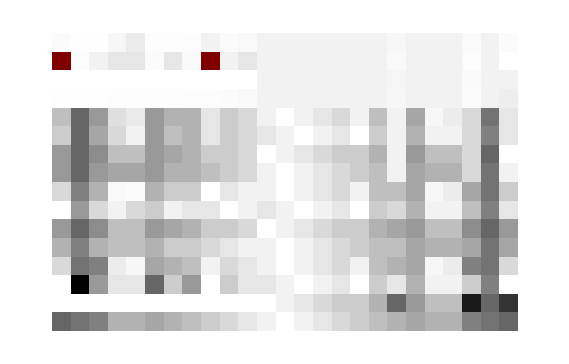

```mathematica
G[12]
```

```mathematica
H[n_]:=Module[{range={-2,-1,1,2}},
Return[Table[F[a,b,x],{a,range},{b,range},{x,-n,n}]]]
```

```mathematica
ListPlot3D[Flatten[H[20],1]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-